```mathematica
(*it = E^((2π* I * D1)/λ) * E^((2π* I * D2)/λ)∫_(d/2 - a/2)^(d/2+a/2) E^((2 π I (w-y1)^2)/(2 * D1 * λ))*E^((2 π I (y1-z)^2)/(2 * D2 * λ))ⅆy1;*)
ib = E^((2π* I * D1)/λ) * E^((2π* I * D2)/λ) ∫_(-d/2-a/2)^(-d/2+a/2) E^((2 π I (w-y2)^2)/(2 * D1 * λ))*E^((2 π I (y2-z)^2)/(2 * D2 * λ))ⅆy2;
```

```mathematica
(*i = (it + ib)*Conjugate[it+ib];
i = (it + ib);
coni = Conjugate[i];
func = i*coni;
i = Conjugate[ib];*)
func =  ib^2;
```

```mathematica
D1 = 380;
D2 = 700;
λ = .000546;
z = x -5.8;
d = .353;
a = .1;
```

```mathematica
func;
realfunc = 10000*Re[func];
```

```mathematica
SetDirectory["/Users/dluntzma/Desktop/DoubleSlit-ED"];
singlefar = Import["20141122_single_slit_far.csv"];
```

```mathematica
fit = NonlinearModelFit[singlefar,realfunc,{{w,0}}, x];
```

NonlinearModelFit::nrlnum: The function value {2.5394, -3.52217, -1.14779, -2.29631, -4.1502, -6.81924, -6.75759, -4.94141, « 35 », -91.2037, -82.9205, -72.9834, -62.004, -74.005, -68.0365, -67.0579, « 24 »} is not a list of real numbers with dimensions {74} at {w} = {0.}.

NonlinearModelFit::nrlnum: The function value {-8.20397, 9.81156, -16.325, 16.1587, -26.7298, 12.8394, -3.36989, -37.4527, « 35 », -97.4339, -120.972, -27.838, -44.2889, -105.116, -103.757, -88.8113, « 24 »} is not a list of real numbers with dimensions {74} at {w} = {0.}.

General::ivar: 0 is not a valid variable.

General::ivar: 0.000204286 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

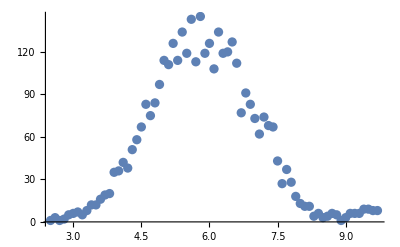

```mathematica
plot = Plot[fit[x], {x, 0, 10},PlotRange->All]
Show[ListPlot[singlefar], plot]
```